# Brendan Philbin Ising Model Minimum Energy

## Import relevant files and define plots

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
numSweeps=Range[0,100];
colors={Darker[Red],Blue,Darker[Green],Black,Orange};
trials=Range[1,50];
plots=Range[1,50];
For[i=1,i≤50,i++,
Evaluate[Symbol["rawTrial" <> ToString[i]]]=Flatten[Import["min_energy_output" <>ToString[i]<>".csv","CSV"]];
Evaluate[Symbol["trial"<>ToString[i]]]=Transpose[{numSweeps,Evaluate[Symbol["rawTrial" <> ToString[i]]]}];
trials⟦i⟧=Evaluate[Symbol["trial"<>ToString[i]]];
Evaluate[Symbol["plot"<>ToString[i]]]=ListLinePlot[trials⟦i⟧,PlotStyle->colors⟦Mod[i,5]⟧];
plots⟦i⟧=Evaluate[Symbol["plot"<>ToString[i]]];
];
```

## Create 10 plots grouping 5 trials with same J_SEED

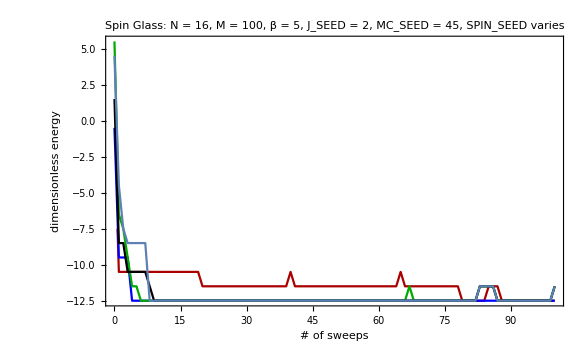

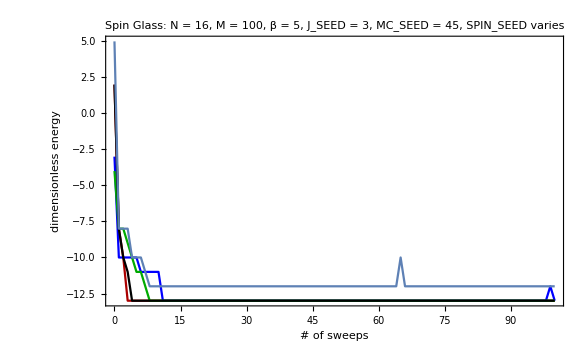

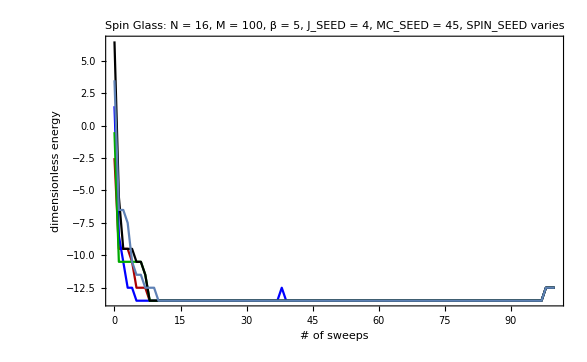

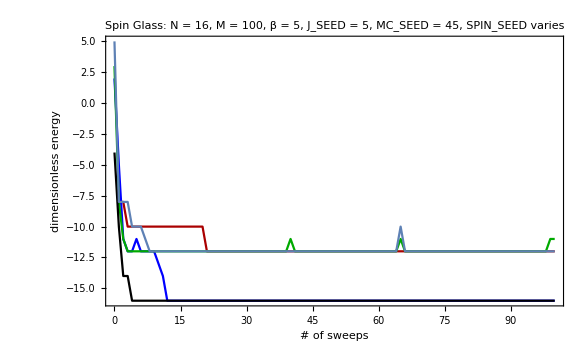

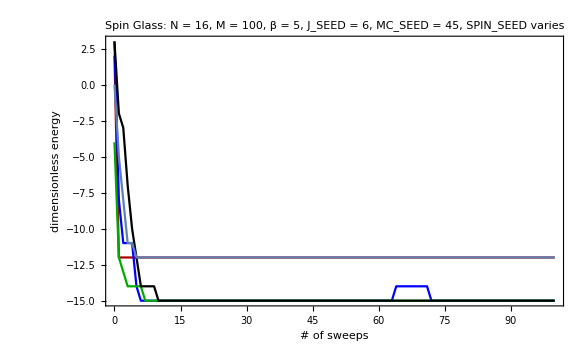

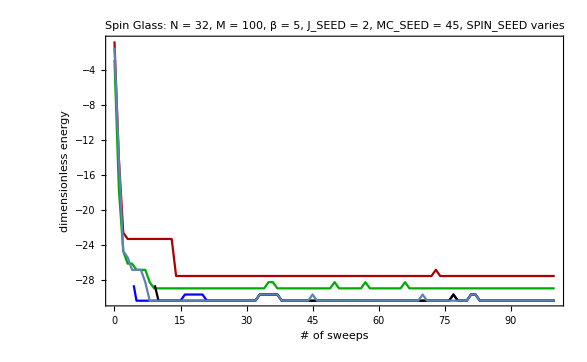

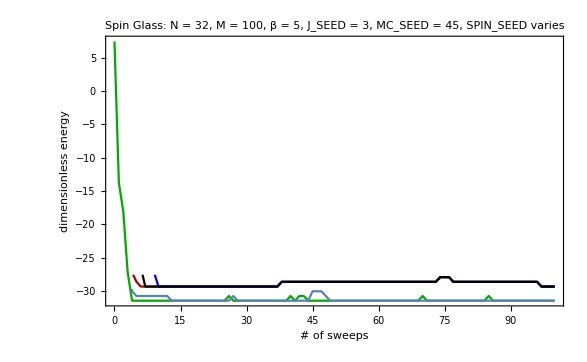

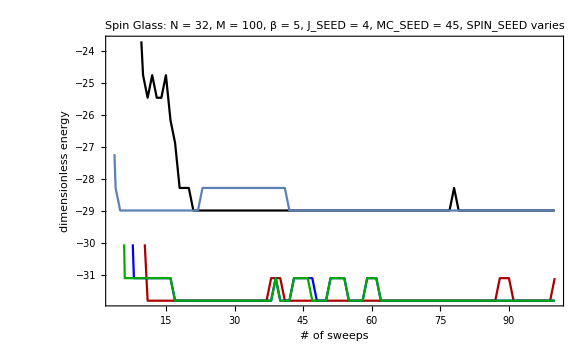

```mathematica
Show[plots⟦1⟧,plots⟦2⟧,plots⟦3⟧,plots⟦4⟧,plots⟦5⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 16, M = 100, β = 5, J_SEED = 2, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦6⟧,plots⟦7⟧,plots⟦8⟧,plots⟦9⟧,plots⟦10⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 16, M = 100, β = 5, J_SEED = 3, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦11⟧,plots⟦12⟧,plots⟦13⟧,plots⟦14⟧,plots⟦15⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 16, M = 100, β = 5, J_SEED = 4, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦16⟧,plots⟦17⟧,plots⟦18⟧,plots⟦19⟧,plots⟦10⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 16, M = 100, β = 5, J_SEED = 5, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦21⟧,plots⟦22⟧,plots⟦23⟧,plots⟦24⟧,plots⟦25⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 16, M = 100, β = 5, J_SEED = 6, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦26⟧,plots⟦27⟧,plots⟦28⟧,plots⟦29⟧,plots⟦30⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 32, M = 100, β = 5, J_SEED = 2, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦31⟧,plots⟦32⟧,plots⟦33⟧,plots⟦34⟧,plots⟦35⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 32, M = 100, β = 5, J_SEED = 3, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦36⟧,plots⟦37⟧,plots⟦38⟧,plots⟦39⟧,plots⟦40⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 32, M = 100, β = 5, J_SEED = 4, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦41⟧,plots⟦42⟧,plots⟦43⟧,plots⟦44⟧,plots⟦45⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 32, M = 100, β = 5, J_SEED = 5, MC_SEED = 45, SPIN_SEED varies"]

Show[plots⟦46⟧,plots⟦47⟧,plots⟦48⟧,plots⟦49⟧,plots⟦50⟧,Frame->True,FrameStyle->Black,LabelStyle->Black,FrameLabel->{"# of sweeps","dimensionless energy"},PlotRange->All,PlotLabel->"Spin Glass: N = 32, M = 100, β = 5, J_SEED = 6, MC_SEED = 45, SPIN_SEED varies"]
```